```mathematica
Clear["Global`*"];
(*SeedRandom[0];*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"sampler2`";
<<"diagnostics`";
```

```mathematica
λ=500 10^-9;
k=2π/λ;
𝒟=1;
d=0.001;
slit1=-d/2;
slit2=d/2;
```

```mathematica
Ia=0.5;
Ib=0.5;
maxw=10^-3;
```

```mathematica
I0=.5;
U1[x_]=-Log[I0 Abs[Exp[I k √((x-slit1)^2+𝒟^2) ]+Exp[I k √((x-slit2)^2+𝒟^2) ]]^2];
U[x_]=-Log[Ia+Ib+2 √(Ia Ib)Cos[k(√((x-slit2)^2+𝒟^2)-√((x-slit1)^2+𝒟^2))]];
U[1]
U1[1]
```

```mathematica
Uq[x_]=N[D1[U[x],{x}]];
Uqq[x_]=N[D2[U[x],{x}]];
outbnd[q_]:=Abs[q[[1]]]>maxw;
```

```mathematica
Dim=1;
BURNIN=5000;
ITERATIONS=10000;
INTERVAL=1001;
PARTICLES=3;
```

```mathematica
qinit=RandomVariate[UniformDistribution[{0,maxw}],{PARTICLES,Dim}];
```

```mathematica
QS=hmc[U,Uq,Uqq,Dim,BURNIN,ITERATIONS,PARTICLES,0,qinit];
```

10014.00355-7.72665-3.72310.0000741398{-3.7231}{0.0000741398}0.2437710.422223{1,4}{2,3,4}True1

20023.88908-7.61219-3.72310.0000741398{-3.7231}{0.0000741398}0.3166960.293574{1,4}{2,3,4}True1

300310.1464-13.8695-3.72310.0000741398{-3.7231}{0.0000741398}0.01399750.0242444{1,4}{2,3,4}True1

400414.3341-18.0572-3.72310.0000741398{-3.7231}{0.0000741398}0.0.{1,4}{2,3,4}True1

50051.42525-5.14836-3.72310.0000741398{-3.7231}{0.0000741398}0.3658180.551375{1,4}{2,3,4}False1

6006-1.09245-2.63066-3.72310.0000741398{-3.7231}{0.0000741398}0.6147620.221831{1,4}{2,3,4}False1

7007-1.23503-2.48808-3.72310.0000741398{-3.7231}{0.0000741398}0.2528550.230891{1,4}{2,3,4}False1

8008-1.6466-2.07651-3.72310.0000741398{-3.7231}{0.0000741398}0.5748710.467659{1,4}{2,3,4}False1

9009-1.88196-1.84115-3.72310.0000741398{-3.7231}{0.0000741398}0.6913760.379053{1,4}{2,3,4}False1

```mathematica
den=NIntegrate[Cos[(π d Sin[ArcTan[x/𝒟]])/λ]^2,{x,-maxw,maxw}];
```

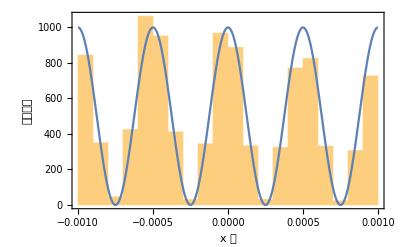

```mathematica
Show[Histogram[QS[[;;,1]],Automatic,"PDF",Frame->True,FrameLabel->{"x 值","概率密度"}],Plot[Cos[(π d Sin[ArcTan[x/𝒟]])/λ]^2/den,{x,-maxw,maxw}]]
```

```mathematica
y=RandomVariate[UniformDistribution[{0,1maxw}],Length[QS]];
```

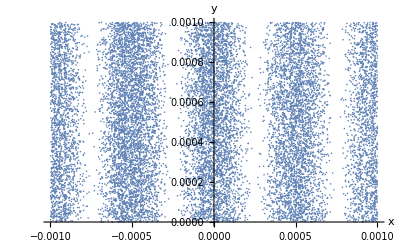

```mathematica
ListPlot[Transpose[{QS[[;;,1]],y}],AxesLabel->{"x","y"}]
```

```mathematica
psrf[QS,PARTICLES]
```

{1.03974}